# MathematicaMVA

MathematicaMVA is a Mathematica package implementing mean-value analysis (MVA) for closed queueing networks in Mathematica. It has been used for researching alternative MVA formulas which also have been implemented in the package.

## Installation

• Download the ["QueueingNetworks.wl"](https://github.com/meteoorkip/MathematicaMVA/raw/master/QueueingNetworks.wl) file.
• Install it as described on ["support.wolfram.com/kb/5648"](http://support.wolfram.com/kb/5648).

## Usage

## 1. Basics

### 1.1 Load the package

Load the package by using:

```mathematica
<<QueueingNetworks`
```

### 1.2 Creating a queueing network

A queueing network can be created using the QueueingNetwork function. The QueueingNetwork function requires a list of stations and a list of routes as arguments.

Stations are represented as a tuple of scheduling and service time. The scheduling can be either FCFS or IS. The service time can be a number or a variable. An FCFS station with service time s1 would be represented as {FCFS,s1}.

Routes are represented as a tuple of the route itself and the routing probability. The route itself is a Rule(→), TwoWayRule(↔), DirectedEdge(->) or a UndirectedEdge(<->) between two station indices (starting from 1). The routing probability can be a number or a variable. A route from station 1 to station 2 with routing probability r12 would be represented as {1→2,r12}.

An example queueing network would be:

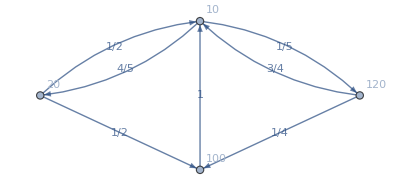

```mathematica
network=QueueingNetwork[
{{FCFS,10},{IS,100},{FCFS,20},{FCFS,120}},{{1->3,4/5},{1->4,1/5},{2->1,1},{3->1,1/2},{3->2,1/2},{4->1,3/4},{4->2,1/4}}
]
```

We will continue to use this queueing network in the examples.

## 2. Retrieving values

### 2.1 Retrieving thee station scheduling

The station scheduling can be retrieved by using the Scheduling function. The Scheduling function requires a queueing network as argument and gives a list of schedules. An index argument can be added to retrieve the scheduling of a single station.

#### 2.1.1 Examples

```mathematica
Scheduling[network]
```

{FCFS,IS,FCFS,FCFS}

```mathematica
Scheduling[network,2]
```

IS

### 2.2 Retrieve the service times

The service times can be retrieved using the ServiceTime function. The ServiceTime function requires a queueing network as argument and gives a list of service times. An index argument can be added to retrieve the service time of a single station.

#### 2.2.1 Examples

```mathematica
ServiceTime[network]
```

{10,100,20,120}

```mathematica
ServiceTime[network,1]
```

10

### 2.3 Retrieve the routing probabilities

The routing probabilities can be retrieved using the RoutingProbability function. The RoutingProbability function requires a queueing network as argument and gives a matrix of routing probabilities. An index argument can be added to retrieve a list of routing probabilities originating from a single station. Another index argument can be added to retrieve the routing probability of a single route.

#### 2.3.1 Examples

```mathematica
RoutingProbability[network]
```

{{0,0,4/5,1/5},{1,0,0,0},{1/2,1/2,0,0},{3/4,1/4,0,0}}

```mathematica
MatrixForm[%]
```

(0 | 0 | 4/5 | 1/5
1 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0
3/4 | 1/4 | 0 | 0)

```mathematica
RoutingProbability[network,1]
```

{0,0,4/5,1/5}

```mathematica
RoutingProbability[network,1,3]
```

4/5

## 3. Calculating values

For the next set of examples we will introduce another queueing network:

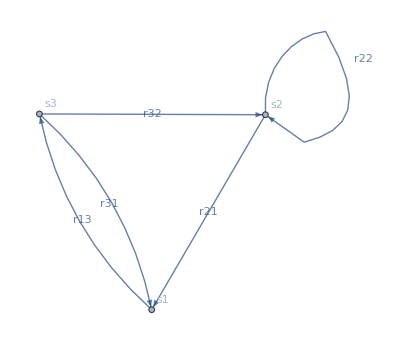

```mathematica
variableNetwork=QueueingNetwork[
{{FCFS,s1},{FCFS,s2},{FCFS,s3}},
{{1->3,r13},{2->1,r21},{2->2,r22},{3->1,r31},{3->2,r32}}
]
```

### 3.1 Calculating the visit counts

The visit counts can be calculated using the VisitCount function. The VisitCount function requires a queueing network as argument and yields a list of visit counts. An index argument can be added to calculate the visit count of a single station.

💡 VisitCount is a ["Functions That Remember Values They Have Found"](https://reference.wolfram.com/language/tutorial/FunctionsThatRememberValuesTheyHaveFound.html) to improve speed.

⚠ Visit count calculation is currently in an experimental state and might yield incorrect results. If needed, visit counts can be manually set using:

```mathematica
VisitCount[network]={v1,v2,v3,v4}
```

#### 3.1.1 Examples

```mathematica
VisitCount[network]
```

{1,9/20,4/5,1/5}

```mathematica
VisitCount[network,4]
```

1/5

```mathematica
VisitCount[variableNetwork]
```

{1,-r32/(-1+r22),1}

### 3.2 Calculating the service demands

The service demands can be calculated using the ServiceDemand function. The ServiceDemand function requires a queueing network as argument and yields a list of service demands. An index argument can be added to calculate the service demand of a single station.

#### 3.2.1 Examples

```mathematica
ServiceDemand[network]
```

{10,45,16,24}

```mathematica
ServiceDemand[network,1]
```

10

```mathematica
ServiceDemand[variableNetwork]
```

{s1,-(r32 s2)/(-1+r22),s3}

### 3.3 Calculating the throughput

The throughput is calculated using the following formula, in a queueing network with M stations and K customers:

X(K)=K·1/(∑_(i=1)^M E[(R̂)_i(K)])

The throughput of the whole queueing network can be calculated using the Throughput function. The Throughput function requires a queueing network and the total number of customers as arguments. The result can be a number or, if there are free variables in the queueing network, an expression.

#### 3.3.1 Examples

```mathematica
Throughput[network,1]
```

1/95

```mathematica
Throughput[network,2]
```

190/9957

```mathematica
Throughput[variableNetwork,1]
```

1/(s1-(r32 s2)/(-1+r22)+s3)

### 3.4 Calculating the expected number of customers

The expected number of customers is calculated using the following formula, in a queueing network with K customers:

E[N_i(K)=X(K)·E[(R̂)_i(K)]

The expected number of customers can be calculated using the ExpectedNumberOfCustomers function. The ExpectedNumberOfCustomers function requires a queueing network and the total number of customers as arguments and yields a list of expected customer counts. An index argument can be added to calculate the expected number of customers of a single station.

#### 3.4.1 Examples

```mathematica
ExpectedNumberOfCustomers[network,1]
```

{2/19,9/19,16/95,24/95}

```mathematica
ExpectedNumberOfCustomers[network,2]
```

{700/3319,2850/3319,1184/3319,1904/3319}

```mathematica
ExpectedNumberOfCustomers[network,1,1]
```

2/19

```mathematica
ExpectedNumberOfCustomers[variableNetwork,1,1]
```

s1/(s1-(r32 s2)/(-1+r22)+s3)

### 3.5 Calculating the expected response time

The expected response time is calculated using the following formula, in a queueing network with K customers; with E[S_i] denoting the service time of station i:

FCFS:E[R_i(K)]=(E[N_i(K-1)]+1)·E[S_i]
IS:E[R_i(K)]=E[S_i]

The expected response time can be calculated using the ExpectedResponseTime function. The ExpectedResponseTime function requires a queueing network and the total number of customers as arguments and yields a list of expected response times. An index argument can be added to calculate the expected response time of a single station.

#### 3.5.1 Examples

```mathematica
ExpectedResponseTime[network,1]
```

{10,100,20,120}

```mathematica
ExpectedResponseTime[network,2]
```

{210/19,100,444/19,2856/19}

```mathematica
ExpectedResponseTime[network,2,2]
```

100

```mathematica
ExpectedResponseTime[variableNetwork,2,2]
```

s2 (1-(r32 s2)/((-1+r22) (s1-(r32 s2)/(-1+r22)+s3)))

### 3.6 Calculating the expected response time per passage

The expected response time per passage is calculated using the following formula, in a queueing network with K customers; with V_i denoting the visit count of station i:

E[(R̂)_i(K)]=E[R_i(K)]·V_i

The expected response time per passage can be calculated using the ExpectedResponseTimePerPassage function. The ExpectedResponseTimePerPassage function requires a queueing network and the total number of customers as arguments and yields a list of expected response times per passage. An index argument can be added to calculate the expected response time per passage of a single station.

#### 3.6.1 Examples

```mathematica
ExpectedResponseTimePerPassage[network,1]
```

{10,45,16,24}

```mathematica
ExpectedResponseTimePerPassage[network,2]
```

{210/19,45,1776/95,2856/95}

```mathematica
ExpectedResponseTimePerPassage[network,1,2]
```

45

```mathematica
ExpectedResponseTimePerPassage[variableNetwork,2,2]
```

-(r32 s2 (1-(r32 s2)/((-1+r22) (s1-(r32 s2)/(-1+r22)+s3))))/(-1+r22)

## 4. Using the formulas

For the next set of examples we will introduce another queueing network:

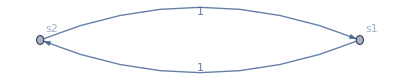

```mathematica
twoFCFSnetwork=QueueingNetwork[
{{FCFS,s1},{FCFS,s2}},
{{1->2,1},{2->1,1}}
]
```

### 4.1 Calculating the state space

The state space uses the following formula, in a queueing network with M stations and K customers:

ℐ(M,K)={(n_1+⋯+n_m)∈ℕ^M|∑_(i=1)^M n_i=K}

The state space can be calculated using the StateSpace function. The StateSpace function requires the number of station and the total number of customers as arguments and yields the state space.

#### 4.1.1 Examples

```mathematica
StateSpace[3,2]
```

{{2,0,0},{0,2,0},{0,0,2},{1,1,0},{1,0,1},{0,1,1}}

```mathematica
StateSpace[2,3]
```

{{3,0},{0,3},{2,1},{1,2}}

### 4.2 Using the 2 FCFS formula

The following formulas have been derived for queueing networks with 2 FCFS stations and K customers; with D_i denoting the service demand of station i:

E[N_a(K)]=(∑_(i=0)^K ((K-i)D_a^(K-1)D_b^i))/(∑_(j=0)^K (D_a^(K-j)D_b^(^j)))
E[(R̂)_a(K)]=(∑_(i=0)^K ((K-i)D_a^(K-i)D_b^i))/(∑_(j=0)^(K-1) (D_a^(K-1-j)D_b^j))

The formulas can be applied with the ExpectedResponseTimePerPassageTwoFCFSFormula and the ExpectedNumberOfCustomersTwoFCFSFormula functions. There are two ways to call these functions.

The first way is by using the queueing network and the total number of customers as arguments. This applies the formula to all stations and returns a list of results. An index argument can be added to apply the formula for a single station

The second way is using the service demand of the first station (a), the service demand of the second station (b) and the total number of customers as arguments. This applies the formula to the first station.

#### 4.2.1 Examples

```mathematica
ExpectedNumberOfCustomersTwoFCFSFormula[twoFCFSnetwork,1]
```

{s1/(s1+s2),s2/(s1+s2)}

```mathematica
ExpectedNumberOfCustomersTwoFCFSFormula[twoFCFSnetwork,2,1]
```

(2 s1^2+s1 s2)/(s1^2+s1 s2+s2^2)

```mathematica
ExpectedNumberOfCustomersTwoFCFSFormula[d1,d2,2]
```

(2 d1^2+d1 d2)/(d1^2+d1 d2+d2^2)

```mathematica
ExpectedResponseTimePerPassageTwoFCFSFormula[twoFCFSnetwork,1]
```

{s1,s2}

```mathematica
ExpectedResponseTimePerPassageTwoFCFSFormula[twoFCFSnetwork,2,2]
```

(s1 s2+2 s2^2)/(s1+s2)

```mathematica
ExpectedResponseTimePerPassageTwoFCFSFormula[d1,d2,2]
```

(2 d1^2+d1 d2)/(d1+d2)

### 4.3 Using the M FCFS formula

The following formulas have been derived for queueing networks with M FCFS stations and K customers; with D_i denoting the service demand of station i:

E[N_i(K)]=(∑_(n∈ℐ(M,K)) (n_i∏_(j=1)^M D_j^n_j))/(∑_(n∈ℐ(M,K)) (∏_(j=1)^M D_j^n_j))
E[(R̂)_i(K)]=(∑_(n∈ℐ(M,K)) (n_i∏_(j=1)^M D_j^n_j))/(∑_(n∈ℐ(M,K)) (∏_(j=1)^M D_j^n_j))

The formulas can be applied with the ExpectedResponseTimePerPassageFCFSFormula and the ExpectedNumberOfCustomersFCFSFormula functions. There are two ways to call these functions.

The first way is by using the queueing network and the total number of customers as arguments. This applies the formula to all stations and returns a list of results. An index argument can be added to apply the formula for a single station.

The second way is using a list of service demands and the total number of customers as arguments. This applies the formula to the first station. An index argument can be added to apply the formula for a single station.

#### 4.3.1 Examples

```mathematica
ExpectedNumberOfCustomersFCFSFormula[twoFCFSnetwork,1]
```

{s1/(s1+s2),s2/(s1+s2)}

```mathematica
ExpectedNumberOfCustomersFCFSFormula[variableNetwork,1,2]
```

-(r32 s2)/((-1+r22) (s1-(r32 s2)/(-1+r22)+s3))

```mathematica
ExpectedNumberOfCustomersFCFSFormula[{d1,d2,d3},1]
```

{d1/(d1+d2+d3),d2/(d1+d2+d3),d3/(d1+d2+d3)}

```mathematica
ExpectedNumberOfCustomersFCFSFormula[{d1,d2,d3},1,2]
```

d2/(d1+d2+d3)

```mathematica
ExpectedResponseTimePerPassageFCFSFormula[twoFCFSnetwork,1]
```

{s1,s2}

```mathematica
ExpectedResponseTimePerPassageFCFSFormula[variableNetwork,1,2]
```

-(r32 s2)/(-1+r22)

```mathematica
ExpectedResponseTimePerPassageFCFSFormula[{d1,d2,d3},1]
```

{d1,d2,d3}

```mathematica
ExpectedResponseTimePerPassageFCFSFormula[{d1,d2,d3},2,1]
```

(2 d1^2+d1 d2+d1 d3)/(d1+d2+d3)

### 4.4 Using the M FCFS and N IS formula

The following formulas for FCFS stations have been derived for queueing networks with M FCFS stations, N IS stations and K customers; with D_i denoting the service demand of station i, M denoting the indices of the FCFS stations and N denoting the indices of the IS stations:

E[N_i(K)]=(∑_(n∈ℐ(M,K)) (K!·n_i·∏_(j∈M) (D_j^n_j)·∏_(j∈N) (D_j^n_j/(n_j!))))/(∑_(n∈ℐ(M,K)) (K!·∏_(j∈M) (D_j^n_j)·∏_(j∈N) (D_j^n_j/(n_j!))))
E[(R̂)_i(K)]=(∑_(n∈ℐ(M,K-1)) ((K-1)!·(n_i+1)D_i·∏_(j∈M) (D_j^n_j)·∏_(j∈N) (D_j^n_j/(n_j!))))/(∑_(n∈ℐ(M,K-1)) ((K-1)!·n_i·∏_(j∈M) (D_j^n_j)·∏_(j∈N) (D_j^n_j/(n_j!))))

The formulas can be applied with the ExpectedResponseTimePerPassageFCFSAndISFormula and the ExpectedNumberOfCustomersFCFSAndISFormula functions. There are two ways to call these functions.

The first way is by using the queueing network and the total number of customers as arguments. This applies the formula to all stations and returns a list of results. An index argument can be added to apply the formula for a single station.

The second way is using a list of service demands, a list of station scheduling and the total number of customers as arguments. This applies the formula to the first station. An index argument can be added to apply the formula for a single station.

#### 4.4.1 Examples

```mathematica
ExpectedNumberOfCustomersFCFSAndISFormula[network,1]
```

{2/19,9/19,16/95,24/95}

```mathematica
ExpectedResponseTimePerPassageFCFSAndISFormula[twoFCFSnetwork,2,1]
```

(2 s1^2+s1 s2)/(s1+s2)

```mathematica
ExpectedNumberOfCustomersFCFSAndISFormula[{d1,d2},{IS,FCFS},1]
```

{d1/(d1+d2),d2/(d1+d2)}

```mathematica
ExpectedNumberOfCustomersFCFSAndISFormula[{d1,d2,d3},{IS,FCFS,FCFS},1,2]
```

d2/(d1+d2+d3)

```mathematica
ExpectedResponseTimePerPassageFCFSAndISFormula[network,1]
```

{10,45,16,24}

```mathematica
ExpectedResponseTimePerPassageFCFSAndISFormula[variableNetwork,1,2]
```

-(r32 s2)/(-1+r22)

```mathematica
ExpectedResponseTimePerPassageFCFSAndISFormula[{10,15},{IS,FCFS},4]
```

{2590/157,7890/157}

```mathematica
ExpectedResponseTimePerPassageFCFSAndISFormula[{10,15,d3},{IS,FCFS,IS},2,2]
```

(600+15 d3)/(25+d3)